Name: GDM_2D_PA.nb
Author: CCL
Date: November 2014
Description: This script generates a 2D Penrose tiling using the generalized dual method. It can also generate a periodic approximant.

```mathematica
tau=(1+Sqrt[5])/2; (*golden ratio*)
tau=2/1;
numlines=10;
tolerance=10^-10;
```

```mathematica
a=2Pi/5;
A=tau-1;
r1={1,0,0};
r2={Cos[a],Sin[a],0};
Or3={Cos[2a],Sin[2a],0};
Or4={Cos[3a],Sin[3a],0};
Or5={Cos[4a],Sin[4a],0};
r3=Normalize[-r1+A r2];
r4=Normalize[-A(r1+r2)];
r5=Normalize[-r2+A r1];
starvectors={r1,r2,r3,r4,r5};
origvectors={r1,r2,Or3,Or4,Or5};
numvectors=Length[starvectors];
startuples=Select[Tuples@{Range[numvectors],Range[numvectors]},Less@@#&];
starbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@starvectors,Axes->True];
origstarbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@origvectors,Axes->True];
xyBasis =Graphics[Arrow[{{0,0},#}]&/@{{1,0},{0,1}},Axes->True];
axes =Graphics3D[Arrow[{{0,0,0},#}]&/@{{1,0,0},{0,1,0},{0,0,1}},Axes->True];
```

```mathematica
PeriodicSeq=Range[-numlines/2,numlines/2];
spacings=PeriodicSeq;
```

```mathematica
p1=0.01;
p2=0.02;
p3=-p1+A p2;
p4=-A(p1+p2);
p5=A p1 - p2;
Phases={p1,p2,p3,p4,p5};
ShiftedSpacings=Table[i+j,{i,Phases},{j,spacings}]
```

{{-4.99,-3.99,-2.99,-1.99,-0.99,0.01,1.01,2.01,3.01,4.01,5.01},{-4.98,-3.98,-2.98,-1.98,-0.98,0.02,1.02,2.02,3.02,4.02,5.02},{-4.99,-3.99,-2.99,-1.99,-0.99,0.01,1.01,2.01,3.01,4.01,5.01},{-5.03,-4.03,-3.03,-2.03,-1.03,-0.03,0.97,1.97,2.97,3.97,4.97},{-5.01,-4.01,-3.01,-2.01,-1.01,-0.01,0.99,1.99,2.99,3.99,4.99}}

```mathematica
maxlength=N[Min[Table[Table[Abs[spacing*Sqrt[2]/starvectors[[i]].{1,1,0}],{spacing,{ShiftedSpacings[[i,1]],ShiftedSpacings[[i,numlines+1]]}}],{i,Range[numvectors]}]]];
```

```mathematica
(*this function finds intersection point of three grid lines, where e_i denotes star vector, and n_i denotes line number*)
FindIntersection[{n1_,e1_},{n2_,e2_},{n3_,e3_}]:=Module[
{p1,p2,p3,d},
p1=n1*e1;
p2=n2*e2;
p3=n3*e3;
d=Det[{e1,e2,e3}];
If[d==0,{0,0,0},
Chop[N[1/d*
((p1.e1)Cross[e2,e3]+(p2.e2)Cross[e3,e1]+(p3.e3)Cross[e1,e2]),{Infinity,150}]]]
]
```

```mathematica
(* ULTIMATE FUNCTION *)
(* finds intersections, with tuples of the form
{{m,n},{i,j},{x,y,z}} = {{indices of spacings},{indices of star vectors},{intersection point}} *)
pts=Table[
{{m,n},
{pair[[1]],pair[[2]]},
FindIntersection[{ShiftedSpacings[[pair[[1]],m]],starvectors[[pair[[1]]]]},{ShiftedSpacings[[pair[[2]],n]],starvectors[[pair[[2]]]]},{0,{0,0,1}}]
},
{m,Range[numlines+1]},{n,Range[numlines+1]},{pair,startuples}];
pts=Flatten[pts,2];
pts=pts[[Ordering[pts[[All,3,2]]]]];
Print[Length[pts]];
```

1210

```mathematica
CountInstances[inlist_,tol_]:=Module[
{poslist,uniqposlist,spacelist,starlist,out,counts,len,uniqlen,counter,curelem,curcompare,i,j},
poslist=inlist[[All,3]];
counts={};
uniqposlist={};
spacelist={};
starlist={};
out={};
len=Length[poslist];
For[i=1,i≤len,i++,
curelem=poslist[[i]];
(*-1 indicates already counted*)
If[TrueQ[curelem==-1],
Continue[];,
uniqposlist=Append[uniqposlist,curelem];
spacelist=Append[spacelist,inlist[[i,1]]];
starlist=Append[starlist,inlist[[i,2]]];
];
counter=1;
For[j=i+1,j≤len,j++,
curcompare=poslist[[j]];
If[TrueQ[curcompare==-1],Continue[];];
If[Norm[poslist[[j]]-curelem]<tol,
poslist[[j]]=-1;(*sets to -1 if counted*)
counter=counter+1;
]
];
counts=Append[counts,counter];
];
uniqlen=Length[uniqposlist];
For[i=1,i≤uniqlen,i++,
out=Append[out,{spacelist[[i]],starlist[[i]],uniqposlist[[i]],counts[[i]]}];
];
out
]
UniqueGridVertices=CountInstances[pts,tolerance];
Print[Length[UniqueGridVertices]];
```

727

```mathematica
UniqueGridVertices[[1]]
```

{{11,11},{1,4},{5.01,-15.3511,0},1}

## Find dual of grid intersections, the quasilattice

```mathematica
(*takes a point and finds the indices of the surrounding grid lines*)
FindGridIndices[x_]:=Module[
{gridindices,curindex,curvector,i},
gridindices={};
Do[
curvector=starvectors[[i]];
curindex=Min[Flatten[Position[ShiftedSpacings[[i]],_?(Chop[#-x.curvector]≥0&)],1]];
(*returns {} if outside bounds of spacings*)
If[TrueQ[curindex==∞],
gridindices={};
Return[{}];
,
gridindices=Append[gridindices,curindex];
];
,{i,Range[numvectors]}
];
Return[gridindices];
]
```

```mathematica
(*constructs PROTOTILE*)
FindProtoTile[vertex_,i_,j_]:=Module[
{v,tile,pair},
v=Table[vertex+y,{y,
{0,origvectors[[i]],origvectors[[j]],
origvectors[[i]]+origvectors[[j]]
}}];
v=v[[All,{1,2}]];
tile=Graphics[Line[{
{v[[1]],v[[2]]},
{v[[1]],v[[3]]},
{v[[2]],v[[4]]},
{v[[3]],v[[4]]}
}]];
pair={i,j};
{tile,pair}
]
```

{5,10,11,5,1}

{5,10,11,5,2}

{5,10,11,5,1}

{5,10,11,5,2}

{}

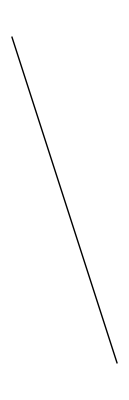
{{10,1},{2,5},{-1.86961,4.83435,0},2}-Graphics-

{{-4.54508,12.0862,0.},-Graphics-,{5}}

```mathematica
(*constructs ZONOTILE*)
eps=10^-3;
UpDown={-1,1};
ProbeIndices=Tuples[{UpDown,UpDown,UpDown,UpDown,UpDown}];
ProbeVectors=N[Table[eps*Normalize[n.starvectors],{n,ProbeIndices}]];

FindZonoTile[vertex_,x_]:=Module[
{GridIndices,UniqueGridIndices,curindex,probe,len,i,j,CurDiff,StarIndex,vertexpair,EdgeIndices,EdgeCoords,VertexCoords,tile,tuple},

(*find grid indices for surrounding open regions*)
GridIndices={};
Do[
curindex=FindGridIndices[x+probe];
Print[curindex];
If[TrueQ[curindex=={}],
Return[{{},{}}];,
GridIndices=Append[GridIndices,curindex];
];
,{probe,ProbeVectors}
];
UniqueGridIndices=Sort[DeleteDuplicates[GridIndices]];
len=Length[UniqueGridIndices];
If[TrueQ[len==0],Return[{{},{}}];];
(*Print[len];*)

(*go through finding connected vertices, and get vertex coordinates*)
EdgeIndices={};
EdgeCoords={};
VertexCoords=ConstantArray[0,len];
VertexCoords[[1]]=vertex;

For[i=1,i≤len,i++,
For[j=i+1,j≤len,j++,
CurDiff=UniqueGridIndices[[j]]-UniqueGridIndices[[i]];
If[Count[CurDiff,1]==1&&Count[CurDiff,-1]==0,
(*Print[i,", ",j,": ",UniqueGridIndices[[i]],", ", UniqueGridIndices[[j]]];*)
StarIndex=Flatten[Position[CurDiff,1]][[1]];
VertexCoords[[j]]=VertexCoords[[i]]+origvectors[[StarIndex]];(*identifies vertex coordinate*)
EdgeIndices=Append[EdgeIndices,{i,j}];
];
];
];

VertexCoords=VertexCoords[[All,{1,2}]];
(*construct tile*)
Do[
EdgeCoords=Append[EdgeCoords,{VertexCoords[[vertexpair[[1]]]],VertexCoords[[vertexpair[[2]]]]}];
,{vertexpair,EdgeIndices}
];
tile=Graphics[Line[EdgeCoords]];

(*find tuple of star vectors*)
tuple={};
For[i=1,i≤numvectors,i++,
If[Length[Tally[UniqueGridIndices[[All,i]]]]>1,
tuple=Append[tuple,i];
]
];

{tile,tuple}
]
testtile=FindTile[UniqueGridVertices[[633]]]
```

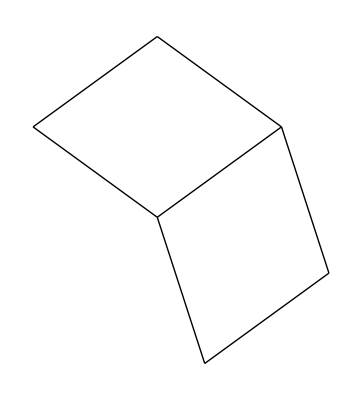
{{2,9},{3,4},{-0.0575173,-4.9737,0},2}-Graphics-

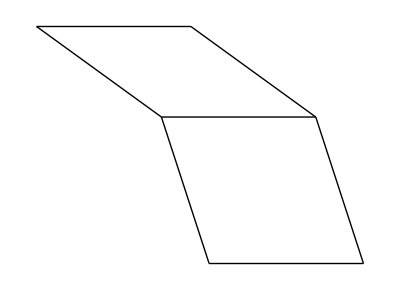
{{6,2},{1,3},{0.01,-4.92465,0},2}-Graphics-

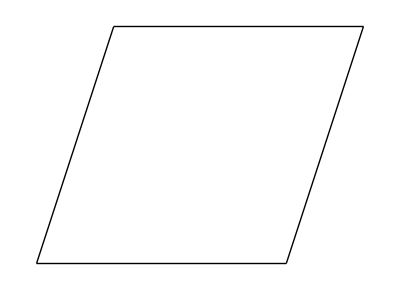
{{5,1},{1,2},{-0.99,-4.91461,0},1}-Graphics-

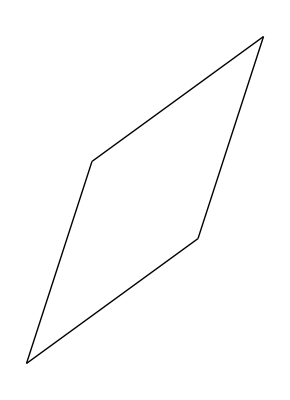
{{1,10},{2,4},{-1.44359,-4.76723,0},1}-Graphics-

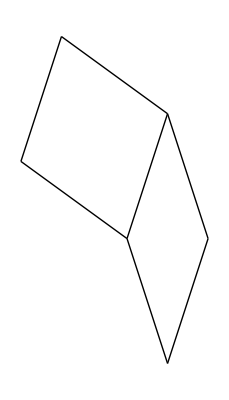
{{1,3},{2,3},{-1.46504,-4.76026,0},2}-Graphics-

{{3,10},{3,4},{-1.45432,-4.75247,0},2}-Graphics-

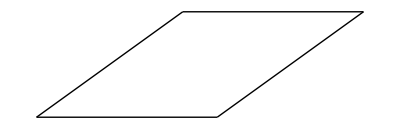
{{7,8},{1,4},{1.01,-4.74171,0},1}-Graphics-

{{4,1},{1,2},{-1.99,-4.58969,0},1}-Graphics-

{{7,2},{1,2},{1.01,-4.51299,0},1}-Graphics-

{{2,8},{2,4},{0.792473,-4.44231,0},1}-Graphics-

{{8,7},{1,4},{2.01,-4.41679,0},1}-Graphics-

{{2,2},{2,3},{0.710526,-4.41568,0},2}-Graphics-

{{5,3},{1,3},{-0.99,-4.41512,0},2}-Graphics-

{{2,8},{3,4},{0.7515,-4.38591,0},2}-Graphics-

{{1,4},{2,3},{-2.64061,-4.37829,0},2}-Graphics-

{{3,11},{1,4},{-2.99,-4.34009,0},1}-Graphics-

{{3,1},{1,2},{-2.99,-4.26477,0},1}-Graphics-

{{1,11},{2,4},{-3.06163,-4.2415,0},1}-Graphics-

{{7,2},{1,3},{1.01,-4.1981,0},2}-Graphics-

{{6,2},{1,2},{0.01,-4.18807,0},1}-Graphics-

{{3,9},{3,4},{-0.645303,-4.16468,0},2}-Graphics-

{{2,3},{2,3},{-0.465044,-4.03372,0},2}-Graphics-

{{4,10},{1,4},{-1.99,-4.01517,0},1}-Graphics-

{{4,10},{3,4},{-2.0421,-3.94345,0},2}-Graphics-

{{2,9},{2,4},{-0.825561,-3.91658,0},1}-Graphics-

{{4,4},{1,3},{-1.99,-3.90559,0},2}-Graphics-

{{5,2},{1,2},{-0.99,-3.86315,0},1}-Graphics-

{{2,7},{3,4},{1.56052,-3.79813,0},2}-Graphics-

{{8,3},{1,2},{2.01,-3.78645,0},1}-Graphics-

{{5,9},{1,4},{-0.99,-3.69025,0},1}-Graphics-

{{3,2},{2,3},{1.71053,-3.68914,0},2}-Graphics-

{{6,3},{1,3},{0.01,-3.68858,0},2}-Graphics-

{{2,4},{2,3},{-1.64061,-3.65175,0},2}-Graphics-

{{3,7},{2,4},{1.41051,-3.59166,0},1}-Graphics-

{{3,8},{3,4},{0.163714,-3.5769,0},2}-Graphics-

{{4,2},{1,2},{-1.99,-3.53823,0},1}-Graphics-

{{8,2},{1,3},{2.01,-3.47156,0},2}-Graphics-

{{7,3},{1,2},{1.01,-3.46153,0},1}-Graphics-

{{3,5},{1,3},{-2.99,-3.39607,0},2}-Graphics-

{{2,10},{2,4},{-2.44359,-3.39085,0},1}-Graphics-

{{6,8},{1,4},{0.01,-3.36533,0},1}-Graphics-

{{4,9},{3,4},{-1.23309,-3.35567,0},2}-Graphics-

{{3,3},{2,3},{0.534956,-3.30718,0},2}-Graphics-

{{2,5},{2,3},{-2.81619,-3.26979,0},2}-Graphics-

{{4,5},{2,4},{3.64658,-3.26674,0},1}-Graphics-

{{3,2},{1,2},{-2.99,-3.21331,0},1}-Graphics-

{{2,6},{3,4},{2.36953,-3.21034,0},2}-Graphics-

{{5,4},{1,3},{-0.99,-3.17905,0},2}-Graphics-

{{6,3},{1,2},{0.01,-3.13661,0},1}-Graphics-

{{5,10},{3,4},{-2.62989,-3.13443,0},2}-Graphics-

{{3,8},{2,4},{-0.207527,-3.06593,0},1}-Graphics-

{{9,4},{1,2},{3.01,-3.0599,0},1}-Graphics-

{{7,7},{1,4},{1.01,-3.04041,0},1}-Graphics-

{{3,7},{3,4},{0.972731,-2.98911,0},2}-Graphics-

{{2,11},{1,4},{-3.99,-2.96371,0},1}-Graphics-

{{4,2},{2,3},{2.71053,-2.9626,0},2}-Graphics-

{{7,3},{1,3},{1.01,-2.96204,0},2}-Graphics-

{{3,4},{2,3},{-0.640615,-2.92521,0},2}-Graphics-

{{2,2},{1,2},{-3.99,-2.88839,0},1}-Graphics-

{{2,6},{2,3},{-3.99176,-2.88782,0},2}-Graphics-

{{2,6},{1,3},{-3.99,-2.88654,0},2}-Graphics-

{{2,11},{2,4},{-4.06163,-2.86512,0},1}-Graphics-

{{5,3},{1,2},{-0.99,-2.81169,0},1}-Graphics-

{{4,8},{3,4},{-0.424071,-2.76788,0},2}-Graphics-

{{9,2},{1,3},{3.01,-2.74502,0},2}-Graphics-

{{4,6},{2,4},{2.02854,-2.74101,0},1}-Graphics-

{{8,4},{1,2},{2.01,-2.73498,0},1}-Graphics-

{{8,6},{1,4},{2.01,-2.71549,0},1}-Graphics-

{{4,5},{1,3},{-1.99,-2.66953,0},2}-Graphics-

{{3,10},{1,4},{-2.99,-2.63879,0},1}-Graphics-

{{2,5},{3,4},{3.17855,-2.62256,0},2}-Graphics-

{{4,3},{2,3},{1.53496,-2.58063,0},2}-Graphics-

{{5,9},{3,4},{-1.82087,-2.54665,0},2}-Graphics-

{{3,5},{2,3},{-1.81619,-2.54324,0},2}-Graphics-

{{3,9},{2,4},{-1.82556,-2.5402,0},1}-Graphics-

{{4,3},{1,2},{-1.99,-2.48677,0},1}-Graphics-

{{6,4},{1,3},{0.01,-2.45251,0},2}-Graphics-

{{5,4},{2,4},{4.26461,-2.41609,0},1}-Graphics-

{{7,4},{1,2},{1.01,-2.41006,0},1}-Graphics-

{{3,6},{3,4},{1.78175,-2.40133,0},2}-Graphics-

{{9,5},{1,4},{3.01,-2.39057,0},1}-Graphics-

{{10,5},{1,2},{4.01,-2.33336,0},1}-Graphics-

{{6,10},{3,4},{-3.21768,-2.32542,0},2}-Graphics-

{{4,9},{1,4},{-1.99,-2.31387,0},1}-Graphics-

{{5,2},{2,3},{3.71053,-2.23606,0},2}-Graphics-

{{8,3},{1,3},{2.01,-2.23549,0},2}-Graphics-

{{4,7},{2,4},{0.410507,-2.21528,0},1}-Graphics-

{{4,4},{2,3},{0.359385,-2.19867,0},2}-Graphics-

{{4,7},{3,4},{0.384946,-2.1801,0},2}-Graphics-

{{3,3},{1,2},{-2.99,-2.16185,0},1}-Graphics-

{{3,6},{2,3},{-2.99176,-2.16128,0},2}-Graphics-

{{3,6},{1,3},{-2.99,-2.16,0},2}-Graphics-

{{6,4},{1,2},{0.01,-2.08514,0},1}-Graphics-

{{10,4},{1,4},{4.01,-2.06565,0},1}-Graphics-

{{2,4},{3,4},{3.98757,-2.03477,0},2}-Graphics-

{{10,2},{1,3},{4.01,-2.01848,0},2}-Graphics-

{{3,10},{2,4},{-3.44359,-2.01447,0},1}-Graphics-

{{9,5},{1,2},{3.01,-2.00844,0},1}-Graphics-

{{5,8},{1,4},{-0.99,-1.98895,0},1}-Graphics-

{{5,8},{3,4},{-1.01186,-1.95886,0},2}-Graphics-

{{5,5},{1,3},{-0.99,-1.94298,0},2}-Graphics-

{{5,5},{2,4},{2.64658,-1.89036,0},1}-Graphics-

{{5,3},{2,3},{2.53496,-1.85409,0},2}-Graphics-

{{2,3},{1,2},{-3.99,-1.83693,0},1}-Graphics-

{{4,5},{2,3},{-0.816185,-1.8167,0},2}-Graphics-

{{3,5},{3,4},{2.59077,-1.81354,0},2}-Graphics-

{{3,5},{2,5},{-4.16733,-1.77931,0},2}-Graphics-

{{5,4},{1,2},{-0.99,-1.76022,0},1}-Graphics-

{{11,3},{1,4},{5.01,-1.74073,0},1}-Graphics-

{{6,9},{3,4},{-2.40866,-1.73763,0},2}-Graphics-

{{7,4},{1,3},{1.01,-1.72597,0},2}-Graphics-

{{4,8},{2,4},{-1.20753,-1.68955,0},1}-Graphics-

{{8,5},{1,2},{2.01,-1.68352,0},1}-Graphics-

{{6,7},{1,4},{0.01,-1.66403,0},1}-Graphics-

{{2,5},{1,5},{-3.99,-1.65048,0},2}-Graphics-

{{11,6},{1,2},{5.01,-1.60682,0},1}-Graphics-

{{4,6},{3,4},{1.19396,-1.59231,0},2}-Graphics-

{{1,11},{1,4},{-4.99,-1.58732,0},1}-Graphics-

{{6,3},{2,4},{4.88264,-1.56544,0},1}-Graphics-

{{7,10},{3,4},{-3.80546,-1.5164,0},2}-Graphics-

{{1,3},{1,2},{-4.99,-1.51201,0},1}-Graphics-

{{6,2},{2,3},{4.71053,-1.50951,0},2}-Graphics-

{{9,3},{1,3},{3.01,-1.50895,0},2}-Graphics-

{{5,4},{2,3},{1.35939,-1.47212,0},2}-Graphics-

{{2,3},{3,4},{4.79658,-1.44699,0},2}-Graphics-

{{4,4},{1,2},{-1.99,-1.43531,0},1}-Graphics-

{{4,6},{2,3},{-1.99176,-1.43473,0},2}-Graphics-

{{4,6},{1,3},{-1.99,-1.43346,0},2}-Graphics-

{{5,7},{3,4},{-0.202839,-1.37108,0},2}-Graphics-

{{5,6},{2,4},{1.02854,-1.36463,0},1}-Graphics-

{{7,5},{1,2},{1.01,-1.3586,0},1}-Graphics-

{{7,6},{1,4},{1.01,-1.33911,0},1}-Graphics-

{{10,6},{1,2},{4.01,-1.2819,0},1}-Graphics-

{{2,10},{1,4},{-3.99,-1.2624,0},1}-Graphics-

{{3,4},{3,4},{3.39978,-1.22576,0},2}-Graphics-

{{6,5},{1,3},{0.01,-1.21644,0},2}-Graphics-

{{4,9},{2,4},{-2.82556,-1.16381,0},1}-Graphics-

{{6,8},{3,4},{-1.59964,-1.14985,0},2}-Graphics-

{{1,4},{1,5},{-4.99,-1.14095,0},2}-Graphics-

{{6,3},{2,3},{3.53496,-1.12755,0},2}-Graphics-

{{3,4},{1,2},{-2.99,-1.11039,0},1}-Graphics-

{{5,5},{2,3},{0.183815,-1.09016,0},2}-Graphics-

{{4,5},{2,5},{-3.16733,-1.05277,0},2}-Graphics-

{{6,4},{2,4},{3.26461,-1.03971,0},1}-Graphics-

{{6,5},{1,2},{0.01,-1.03368,0},1}-Graphics-

{{8,5},{1,4},{2.01,-1.01419,0},1}-Graphics-

{{4,5},{3,4},{2.00298,-1.00453,0},2}-Graphics-

{{8,4},{1,3},{2.01,-0.999425,0},2}-Graphics-

{{9,6},{1,2},{3.01,-0.956979,0},1}-Graphics-

{{3,9},{1,4},{-2.99,-0.937484,0},1}-Graphics-

{{7,9},{3,4},{-2.99644,-0.928615,0},2}-Graphics-

{{3,5},{1,5},{-2.99,-0.923934,0},2}-Graphics-

{{5,7},{2,4},{-0.589493,-0.838895,0},1}-Graphics-

{{2,4},{1,2},{-3.99,-0.785466,0},1}-Graphics-

{{5,6},{3,4},{0.606178,-0.783293,0},2}-Graphics-

{{10,3},{1,3},{4.01,-0.782408,0},2}-Graphics-

{{6,4},{2,3},{2.35939,-0.745582,0},2}-Graphics-

{{5,5},{1,2},{-0.99,-0.708762,0},1}-Graphics-

{{5,6},{2,3},{-0.991756,-0.708192,0},2}-Graphics-

{{8,10},{3,4},{-4.39325,-0.707383,0},2}-Graphics-

{{5,6},{1,3},{-0.99,-0.706916,0},2}-Graphics-

{{9,4},{1,4},{3.01,-0.689267,0},1}-Graphics-

{{4,4},{2,5},{-4.3429,-0.670803,0},2}-Graphics-

{{4,10},{2,4},{-4.44359,-0.638084,0},1}-Graphics-

{{3,3},{3,4},{4.2088,-0.637971,0},2}-Graphics-

{{8,6},{1,2},{2.01,-0.632059,0},1}-Graphics-

{{4,8},{1,4},{-1.99,-0.612564,0},1}-Graphics-

{{6,7},{3,4},{-0.790624,-0.562062,0},2}-Graphics-

{{11,7},{1,2},{5.01,-0.555356,0},1}-Graphics-

{{6,5},{2,4},{1.64658,-0.513975,0},1}-Graphics-

{{7,5},{1,3},{1.01,-0.489899,0},2}-Graphics-

{{1,4},{1,2},{-4.99,-0.460546,0},1}-Graphics-

{{4,4},{3,4},{2.812,-0.41674,0},2}-Graphics-

{{2,4},{1,5},{-3.99,-0.414408,0},2}-Graphics-

{{7,3},{2,3},{4.53496,-0.401005,0},2}-Graphics-

{{4,5},{1,2},{-1.99,-0.383843,0},1}-Graphics-

{{10,3},{1,4},{4.01,-0.364348,0},1}-Graphics-

{{6,5},{2,3},{1.18381,-0.363616,0},2}-Graphics-

{{7,8},{3,4},{-2.18743,-0.34083,0},2}-Graphics-

{{5,5},{2,5},{-2.16733,-0.326226,0},2}-Graphics-

{{5,8},{2,4},{-2.20753,-0.313164,0},1}-Graphics-

{{7,6},{1,2},{1.01,-0.30714,0},1}-Graphics-

{{5,7},{1,4},{-0.99,-0.287644,0},1}-Graphics-

{{9,4},{1,3},{3.01,-0.272882,0},2}-Graphics-

{{10,7},{1,2},{4.01,-0.230437,0},1}-Graphics-

{{4,5},{1,5},{-1.99,-0.197391,0},2}-Graphics-

{{5,5},{3,4},{1.41519,-0.195508,0},2}-Graphics-

{{7,3},{2,4},{3.88264,-0.189056,0},1}-Graphics-

{{8,9},{3,4},{-3.58423,-0.119598,0},2}-Graphics-

{{3,5},{1,2},{-2.99,-0.0589231,0},1}-Graphics-

{{11,2},{1,4},{5.01,-0.0394279,0},1}-Graphics-

{{7,4},{2,3},{3.35939,-0.019039,0},2}-Graphics-

{{6,6},{2,4},{0.028541,0.0117557,0},1}-Graphics-

{{6,6},{1,2},{0.01,0.01778,0},1}-Graphics-

{{6,6},{2,3},{0.00824429,0.0183505,0},2}-Graphics-

{{6,6},{1,3},{0.01,0.0196261,0},2}-Graphics-

{{6,6},{3,4},{0.0183927,0.0257237,0},2}-Graphics-

{{6,6},{1,4},{0.01,0.0372752,0},1}-Graphics-

{{5,4},{2,5},{-3.3429,0.05574,0},2}-Graphics-

{{9,7},{1,2},{3.01,0.0944832,0},1}-Graphics-

{{1,3},{1,5},{-4.99,0.0951174,0},2}-Graphics-

{{9,10},{3,4},{-4.98103,0.101634,0},2}-Graphics-

{{1,10},{1,4},{-4.99,0.113978,0},1}-Graphics-

{{3,8},{4,5},{3.62101,0.171045,0},2}-Graphics-

{{5,9},{2,4},{-3.82556,0.212567,0},1}-Graphics-

{{8,5},{1,3},{2.01,0.236643,0},2}-Graphics-

{{7,5},{4,5},{-1.37841,0.246955,0},2}-Graphics-

{{2,5},{1,2},{-3.99,0.265997,0},1}-Graphics-

{{3,4},{1,5},{-2.99,0.312134,0},2}-Graphics-

{{7,4},{2,4},{2.26461,0.336675,0},1}-Graphics-

{{5,6},{1,2},{-0.99,0.3427,0},1}-Graphics-

{{7,5},{1,4},{1.01,0.362195,0},1}-Graphics-

{{7,5},{2,3},{2.18381,0.362927,0},2}-Graphics-

{{4,7},{4,5},{2.22421,0.392277,0},2}-Graphics-

{{6,5},{2,5},{-1.16733,0.400317,0},2}-Graphics-

{{8,7},{1,2},{2.01,0.419403,0},1}-Graphics-

{{5,3},{2,5},{-4.51847,0.437706,0},2}-Graphics-

{{2,9},{1,4},{-3.99,0.438898,0},1}-Graphics-

{{10,4},{1,3},{4.01,0.45366,0},2}-Graphics-

{{8,4},{4,5},{-2.77521,0.468187,0},2}-Graphics-

{{11,8},{1,2},{5.01,0.496106,0},1}-Graphics-

{{5,5},{1,5},{-0.99,0.529152,0},2}-Graphics-

{{6,7},{2,4},{-1.58949,0.537487,0},1}-Graphics-

{{1,5},{1,2},{-4.99,0.590916,0},1}-Graphics-

{{5,6},{4,5},{0.82741,0.613509,0},2}-Graphics-

{{8,2},{2,4},{4.50068,0.661595,0},1}-Graphics-

{{4,6},{1,2},{-1.99,0.667619,0},1}-Graphics-

{{8,4},{1,4},{2.01,0.687115,0},1}-Graphics-

{{9,3},{4,5},{-4.17201,0.689419,0},2}-Graphics-

{{8,4},{2,3},{4.35939,0.707504,0},2}-Graphics-

{{7,7},{1,2},{1.01,0.744323,0},1}-Graphics-

{{7,6},{2,3},{1.00824,0.744893,0},2}-Graphics-

{{7,6},{1,3},{1.01,0.746169,0},2}-Graphics-

{{2,8},{4,5},{4.43003,0.758831,0},2}-Graphics-

{{3,8},{1,4},{-2.99,0.763818,0},1}-Graphics-

{{6,4},{2,5},{-2.3429,0.782283,0},2}-Graphics-

{{10,8},{1,2},{4.01,0.821026,0},1}-Graphics-

{{2,3},{1,5},{-3.99,0.82166,0},2}-Graphics-

{{6,5},{4,5},{-0.569393,0.834741,0},2}-Graphics-

{{7,5},{2,4},{0.646575,0.862407,0},1}-Graphics-

{{9,5},{1,3},{3.01,0.963186,0},2}-Graphics-

{{3,7},{4,5},{3.03323,0.980062,0},2}-Graphics-

{{3,6},{1,2},{-2.99,0.992539,0},1}-Graphics-

{{9,3},{1,4},{3.01,1.01203,0},1}-Graphics-

{{4,4},{1,5},{-1.99,1.03868,0},2}-Graphics-

{{7,4},{4,5},{-1.96619,1.05597,0},2}-Graphics-

{{6,8},{2,4},{-3.20753,1.06322,0},1}-Graphics-

{{6,7},{1,2},{0.01,1.06924,0},1}-Graphics-

{{4,7},{1,4},{-1.99,1.08874,0},1}-Graphics-

{{8,5},{2,3},{3.18381,1.08947,0},2}-Graphics-

{{7,5},{2,5},{-0.167326,1.12686,0},2}-Graphics-

{{9,8},{1,2},{3.01,1.14595,0},1}-Graphics-

{{6,3},{2,5},{-3.51847,1.16425,0},2}-Graphics-

{{8,3},{2,4},{2.88264,1.18733,0},1}-Graphics-

{{4,6},{4,5},{1.63643,1.20129,0},2}-Graphics-

{{6,5},{1,5},{0.01,1.25569,0},2}-Graphics-

{{8,3},{4,5},{-3.363,1.2772,0},2}-Graphics-

{{2,6},{1,2},{-3.99,1.31746,0},1}-Graphics-

{{1,2},{1,5},{-4.99,1.33119,0},2}-Graphics-

{{10,2},{1,4},{4.01,1.33695,0},1}-Graphics-

{{7,6},{2,4},{-0.971459,1.38814,0},1}-Graphics-

{{5,7},{1,2},{-0.99,1.39416,0},1}-Graphics-

{{5,6},{1,4},{-0.99,1.41366,0},1}-Graphics-

{{5,5},{4,5},{0.239624,1.42253,0},2}-Graphics-

{{8,8},{1,2},{2.01,1.47087,0},1}-Graphics-

{{8,6},{2,3},{2.00824,1.47144,0},2}-Graphics-

{{8,6},{1,3},{2.01,1.47271,0},2}-Graphics-

{{9,2},{4,5},{-4.7598,1.49844,0},2}-Graphics-

{{7,4},{2,5},{-1.3429,1.50883,0},2}-Graphics-

{{6,2},{2,5},{-4.69404,1.54621,0},2}-Graphics-

{{11,9},{1,2},{5.01,1.54757,0},1}-Graphics-

{{3,3},{1,5},{-2.99,1.5482,0},2}-Graphics-

{{2,7},{4,5},{3.84225,1.56785,0},2}-Graphics-

{{6,9},{2,4},{-4.82556,1.58895,0},1}-Graphics-

{{1,6},{1,2},{-4.99,1.64238,0},1}-Graphics-

{{6,4},{4,5},{-1.15718,1.64376,0},2}-Graphics-

{{11,1},{1,4},{5.01,1.66187,0},1}-Graphics-

{{10,5},{1,3},{4.01,1.68973,0},2}-Graphics-

{{8,4},{2,4},{1.26461,1.71306,0},1}-Graphics-

{{4,7},{1,2},{-1.99,1.71908,0},1}-Graphics-

{{6,5},{1,4},{0.01,1.73858,0},1}-Graphics-

{{5,4},{1,5},{-0.99,1.76522,0},2}-Graphics-

{{3,6},{4,5},{2.44544,1.78908,0},2}-Graphics-

{{7,8},{1,2},{1.01,1.79578,0},1}-Graphics-

{{1,9},{1,4},{-4.99,1.81528,0},1}-Graphics-

{{9,5},{2,3},{4.18381,1.81601,0},2}-Graphics-

{{8,5},{2,5},{0.832674,1.8534,0},2}-Graphics-

{{7,3},{4,5},{-2.55398,1.86499,0},2}-Graphics-

{{10,9},{1,2},{4.01,1.87249,0},1}-Graphics-

{{7,3},{2,5},{-2.51847,1.89079,0},2}-Graphics-

{{7,7},{2,4},{-2.58949,1.91387,0},1}-Graphics-

{{7,5},{1,5},{1.01,1.98224,0},2}-Graphics-

{{4,5},{4,5},{1.04864,2.01031,0},2}-Graphics-

{{9,2},{2,4},{3.50068,2.03798,0},1}-Graphics-

{{3,7},{1,2},{-2.99,2.044,0},1}-Graphics-

{{2,2},{1,5},{-3.99,2.05773,0},2}-Graphics-

{{7,4},{1,4},{1.01,2.0635,0},1}-Graphics-

{{8,2},{4,5},{-3.95078,2.08622,0},2}-Graphics-

{{6,8},{1,2},{0.01,2.1207,0},1}-Graphics-

{{2,8},{1,4},{-3.99,2.1402,0},1}-Graphics-

{{1,7},{4,5},{4.65126,2.15563,0},2}-Graphics-

{{9,9},{1,2},{3.01,2.19741,0},1}-Graphics-

{{9,6},{2,3},{3.00824,2.19798,0},2}-Graphics-

{{9,6},{1,3},{3.01,2.19925,0},2}-Graphics-

{{5,4},{4,5},{-0.348161,2.23154,0},2}-Graphics-

{{8,4},{2,5},{-0.342897,2.23537,0},2}-Graphics-

{{8,5},{2,4},{-0.353425,2.23879,0},1}-Graphics-

{{7,2},{2,5},{-3.69404,2.27276,0},2}-Graphics-

{{4,3},{1,5},{-1.99,2.27474,0},2}-Graphics-

{{2,7},{1,2},{-3.99,2.36892,0},1}-Graphics-

{{2,6},{4,5},{3.25446,2.37686,0},2}-Graphics-

{{8,3},{1,4},{2.01,2.38842,0},1}-Graphics-

{{7,8},{2,4},{-4.20753,2.4396,0},1}-Graphics-

{{5,8},{1,2},{-0.99,2.44562,0},1}-Graphics-

{{6,3},{4,5},{-1.74496,2.45277,0},2}-Graphics-

{{3,7},{1,4},{-2.99,2.46512,0},1}-Graphics-

{{6,4},{1,5},{0.01,2.49176,0},2}-Graphics-

{{8,9},{1,2},{2.01,2.52233,0},1}-Graphics-

{{9,3},{2,4},{1.88264,2.56371,0},1}-Graphics-

{{1,1},{1,5},{-4.99,2.56725,0},2}-Graphics-

{{9,5},{2,5},{1.83267,2.57994,0},2}-Graphics-

{{3,5},{4,5},{1.85766,2.5981,0},2}-Graphics-

{{11,10},{1,2},{5.01,2.59903,0},1}-Graphics-

{{8,3},{2,5},{-1.51847,2.61733,0},2}-Graphics-

{{7,1},{2,5},{-4.86961,2.65472,0},2}-Graphics-

{{7,2},{4,5},{-3.14177,2.67401,0},2}-Graphics-

{{8,5},{1,5},{2.01,2.70878,0},2}-Graphics-

{{9,2},{1,4},{3.01,2.71334,0},1}-Graphics-

{{8,6},{2,4},{-1.97146,2.76452,0},1}-Graphics-

{{4,8},{1,2},{-1.99,2.77054,0},1}-Graphics-

{{3,2},{1,5},{-2.99,2.78427,0},2}-Graphics-

{{4,6},{1,4},{-1.99,2.79004,0},1}-Graphics-

{{4,4},{4,5},{0.460856,2.81933,0},2}-Graphics-

{{7,9},{1,2},{1.01,2.84725,0},1}-Graphics-

{{10,1},{2,4},{4.11871,2.88863,0},1}-Graphics-

{{8,1},{4,5},{-4.53857,2.89524,0},2}-Graphics-

{{10,10},{1,2},{4.01,2.92395,0},1}-Graphics-

{{10,6},{2,3},{4.00824,2.92452,0},2}-Graphics-

{{10,6},{1,3},{4.01,2.9258,0},2}-Graphics-

{{9,4},{2,5},{0.657103,2.96191,0},2}-Graphics-

{{1,6},{4,5},{4.06348,2.96465,0},2}-Graphics-

{{8,2},{2,5},{-2.69404,2.9993,0},2}-Graphics-

{{5,3},{1,5},{-0.99,3.00129,0},2}-Graphics-

{{10,1},{1,4},{4.01,3.03826,0},1}-Graphics-

{{5,3},{4,5},{-0.935946,3.04056,0},2}-Graphics-

{{9,4},{2,4},{0.264609,3.08944,0},1}-Graphics-

{{3,8},{1,2},{-2.99,3.09546,0},1}-Graphics-

{{5,5},{1,4},{-0.99,3.11496,0},1}-Graphics-

{{6,9},{1,2},{0.01,3.17217,0},1}-Graphics-

{{2,5},{4,5},{2.66668,3.18588,0},2}-Graphics-

{{7,4},{1,5},{1.01,3.2183,0},2}-Graphics-

{{9,10},{1,2},{3.01,3.24887,0},1}-Graphics-

{{6,2},{4,5},{-2.33275,3.26179,0},2}-Graphics-

{{8,7},{2,4},{-3.58949,3.29025,0},1}-Graphics-

{{2,1},{1,5},{-3.99,3.2938,0},2}-Graphics-

{{10,5},{2,5},{2.83267,3.30649,0},2}-Graphics-

{{9,3},{2,5},{-0.518467,3.34388,0},2}-Graphics-

{{8,1},{2,5},{-3.86961,3.38127,0},2}-Graphics-

{{3,4},{4,5},{1.26987,3.40711,0},2}-Graphics-

{{10,2},{2,4},{2.50068,3.41436,0},1}-Graphics-

{{9,5},{1,5},{3.01,3.43532,0},2}-Graphics-

{{6,4},{1,4},{0.01,3.43988,0},1}-Graphics-

{{7,1},{4,5},{-3.72955,3.48302,0},2}-Graphics-

{{5,9},{1,2},{-0.99,3.49709,0},1}-Graphics-

{{4,2},{1,5},{-1.99,3.51081,0},2}-Graphics-

{{8,10},{1,2},{2.01,3.57379,0},1}-Graphics-

{{9,5},{2,4},{-1.35342,3.61517,0},1}-Graphics-

{{4,3},{4,5},{-0.126929,3.62835,0},2}-Graphics-

{{11,11},{1,2},{5.01,3.65049,0},1}-Graphics-

{{11,6},{2,3},{5.00824,3.65106,0},2}-Graphics-

{{10,4},{2,5},{1.6571,3.68845,0},2}-Graphics-

{{9,2},{2,5},{-1.69404,3.72584,0},2}-Graphics-

{{6,3},{1,5},{0.01,3.72783,0},2}-Graphics-

{{7,3},{1,4},{1.01,3.7648,0},1}-Graphics-

{{1,5},{4,5},{3.47569,3.77367,0},2}-Graphics-

{{4,9},{1,2},{-1.99,3.82201,0},1}-Graphics-

{{5,2},{4,5},{-1.52373,3.84958,0},2}-Graphics-

{{7,10},{1,2},{1.01,3.89871,0},1}-Graphics-

{{10,3},{2,4},{0.882643,3.94009,0},1}-Graphics-

{{8,4},{1,5},{2.01,3.94485,0},2}-Graphics-

{{10,11},{1,2},{4.01,3.97541,0},1}-Graphics-

{{2,4},{4,5},{2.07889,3.9949,0},2}-Graphics-

{{3,1},{1,5},{-2.99,4.02034,0},2}-Graphics-

{{11,5},{2,5},{3.83267,4.03303,0},2}-Graphics-

{{10,3},{2,5},{0.481533,4.07042,0},2}-Graphics-

{{6,1},{4,5},{-2.92053,4.07081,0},2}-Graphics-

{{8,2},{1,4},{2.01,4.08972,0},1}-Graphics-

{{9,1},{2,5},{-2.86961,4.10781,0},2}-Graphics-

{{3,3},{4,5},{0.682088,4.21613,0},2}-Graphics-

{{6,10},{1,2},{0.01,4.22363,0},1}-Graphics-

{{5,2},{1,5},{-0.99,4.23736,0},2}-Graphics-

{{11,1},{2,4},{3.11871,4.26501,0},1}-Graphics-

{{9,11},{1,2},{3.01,4.30033,0},1}-Graphics-

{{11,4},{2,5},{2.6571,4.415,0},2}-Graphics-

{{4,2},{4,5},{-0.714714,4.43736,0},2}-Graphics-

{{10,2},{2,5},{-0.694038,4.45238,0},2}-Graphics-

{{7,3},{1,5},{1.01,4.45437,0},2}-Graphics-

{{10,4},{2,4},{-0.735391,4.46582,0},1}-Graphics-

{{4,5},{1,4},{-1.99,4.49134,0},1}-Graphics-

{{5,10},{1,2},{-0.99,4.54855,0},1}-Graphics-

{{8,11},{1,2},{2.01,4.62525,0},1}-Graphics-

{{5,1},{4,5},{-2.11152,4.65859,0},2}-Graphics-

{{4,1},{1,5},{-1.99,4.74688,0},2}-Graphics-

{{11,2},{2,4},{1.50068,4.79074,0},1}-Graphics-

{{11,3},{2,5},{1.48153,4.79696,0},2}-Graphics-

{{5,4},{1,4},{-0.99,4.81626,0},1}-Graphics-

{{10,1},{2,5},{-1.86961,4.83435,0},2}-Graphics-

{{7,11},{1,2},{1.01,4.95017,0},1}-Graphics-

{{6,2},{1,5},{0.01,4.9639,0},2}-Graphics-

{{3,2},{4,5},{0.0943026,5.02515,0},2}-Graphics-

```mathematica
FindTile[pt_]:=Module[
{l,m,i,j,x,count,vertex,tile,tuple,v,indices},
l=pt[[1,1]];
m=pt[[1,2]];
i=pt[[2,1]];
j=pt[[2,2]];
x=pt[[3]];
count=pt[[4]];
If[Abs[x[[1]]]<maxlength&&Abs[x[[2]]]<maxlength&&Abs[x[[3]]]<maxlength,
indices=FindGridIndices[x];
If[TrueQ[indices!={}]&&VectorQ[N[indices.origvectors],NumericQ],
vertex=N[indices.origvectors];
If[TrueQ[count==1],
{tile,tuple}=FindProtoTile[vertex,i,j];,
{tile,tuple}=FindZonoTile[vertex,x];
];
If[TrueQ[tuple=={}],
Return[];
];
Print[pt,tile];
Return[{vertex,tile,tuple}]
];

];

Return[];
]
tiles=Select[Table[FindTile[pt],{pt,UniqueGridVertices}],UnsameQ[#,Null]&];
```

```mathematica
Position[tiles[[All,3]],_?(Length[#]==1&)]
```

{{325},{336},{358},{363},{370},{384},{386},{388},{394},{402},{405},{407}}

```mathematica
Position[UniqueGridVertices[[All,1]],{10,1}]
```

{{47},{168},{425},{471},{539},{549},{633},{712}}

```mathematica
UniqueGridVertices[[460]]
```

{{6,2},{2,5},{-4.69404,1.54621,0},2}

## Plotting

```mathematica
Module[
{i,counts},
counts=Table[Length[tiles[[x,3]]],{x,Range[1,Length[tiles]]}];
For[i=5,i≥0,i--,
Print["# tiles formed form intersection of ", i, " grid lines: ", Count[counts,i]];
]
]
```

# tiles formed form intersection of 5 grid lines: 0

# tiles formed form intersection of 4 grid lines: 0

# tiles formed form intersection of 3 grid lines: 205

# tiles formed form intersection of 2 grid lines: 193

# tiles formed form intersection of 1 grid lines: 12

# tiles formed form intersection of 0 grid lines: 0

```mathematica
Show[xyBasis,
Table[Plot[-starvectors[[i,1]]/starvectors[[i,2]]*x+ShiftedSpacings[[i,j]]/starvectors[[i,2]],{x,-maxlength,maxlength},PlotStyle->{Blue,Thin}],{i,Range[2,5]},{j,Range[numlines+1]}],
Table[Graphics[{Blue,Thin,Line[{{x,-maxlength},{x,maxlength}}]}],{x,ShiftedSpacings[[1]]}],
Graphics[{Green,Opacity[0.3],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],
Graphics[{PointSize[0.005],Point[UniqueGridVertices[[All,3,{1,2}]]]}](*option here gets rid of indeterminate values*),
Graphics[{PointSize[0.001],Red,Point[UniqueGridVertices[[186,3,{1,2}]]]}],
AspectRatio->1,PlotRange->{{-1.25maxlength,1.25maxlength},{-1.25maxlength,1.25maxlength}}
]
```

-Graphics-

```mathematica
(*translate vertices and tiles so that COM is at origin*)
CalculateCOM[pts_]:=Module[
{x,y},
x=0;y=0;
Do[
x+=pt[[1]];y+=pt[[2]];,
{pt,pts}];
{x,y}/Length[pts]
]
com=CalculateCOM[Flatten[tiles[[All,2,1,1]],2]];
tiles2=tiles;
tiles2[[All,1]]=Table[x-com,{x,tiles2[[All,1,{1,2}]]}];
translate={com,com};
Do[
tiles2[[i,2,1,1]]=Table[x-translate,{x,tiles2[[i,2,1,1,All]]}];
,{i,Length[tiles2]}
]
```

```mathematica
allvertices=Module[
{list,n},
list={};
n=Length[tiles2];
Do[
list=Join[list,Flatten[tiles2[[i,2,1,1]],1]];
,{i,Range[n]}
];
list
];
```

```mathematica
GraphicsRow[
{
Show[xyBasis,
(*tiles2[[All,2]],*)
Graphics[{PointSize[0.01],Red,Point[tiles2[[All,1]]]}],
Graphics[{PointSize[0.01],Blue,Point[allvertices]}],
AspectRatio->1,ImageSize->600
],
Show[xyBasis,
tiles2[[All,2]],
Graphics[{PointSize[0.01],Red,Point[tiles2[[All,1]]]}],
AspectRatio->1,ImageSize->600
]
}]
```

-Graphics-